## Some setting

Data

```mathematica
xn={-27.02,3.57,8.191,9.898,9.603,9.945,10.056}
```

{-27.02,3.57,8.191,9.898,9.603,9.945,10.056}

Sample mean

```mathematica
Mean[xn]
```

3.46329

Normalizing constant

```mathematica
∫_(-∞)^∞ Exp[(-N(μ-x)^2)/(2 σ^2)]ⅆμ
```

ConditionalExpression[(√(2 π))/(√(N/σ^2)),Re[N/σ^2]≥0]

## Posterior distribution function w.o. normalizing constant

```mathematica
∫_0^∞ σ^c Exp[(-(x-μ)^2)/(2 σ^2)-σ/s]ⅆσ
```

```mathematica
ConditionalExpression[11.976796597153522 HypergeometricPFQ[{},{-0.050000000000000044,0.44999999999999996},-1/800 (x-μ)^2]-(1.2220697972757049 HypergeometricPFQ[{},{1.55,0.5},-1/800 (x-μ)^2])/((1/(x-μ)^2)^0.55)-(0.47443725266903375 HypergeometricPFQ[{},{2.05,1.4999999999999998},-1/800 (x-μ)^2])/((1/(x-μ)^2)^1.05),Re[(x-μ)^2]>0]/.x->10
```

ConditionalExpression[11.9768 HypergeometricPFQ[{},{-0.05,0.45},-1/800 (10-μ)^2]-(1.22207 HypergeometricPFQ[{},{1.55,0.5},-1/800 (10-μ)^2])/((1/(10-μ)^2)^0.55)-(0.474437 HypergeometricPFQ[{},{2.05,1.5},-1/800 (10-μ)^2])/((1/(10-μ)^2)^1.05),Re[(10-μ)^2]>0]

```mathematica
Assuming[Re[(x-μ)^2]>0,∫_0^∞ σ^0.1 Exp[-(x-μ)^2/(2 σ^2)]Exp[-σ/10]ⅆσ]
```

Define function for posterior distribution of one data

```mathematica
Clear[plot]
```

```mathematica
plot[x_]:=11.976796597153522 HypergeometricPFQ[{},{-0.050000000000000044,0.44999999999999996},-1/800 (x-μ)^2]-(1.2220697972757049 HypergeometricPFQ[{},{1.55,0.5},-1/800 (x-μ)^2])/((1/(x-μ)^2)^0.55)-(0.47443725266903375 HypergeometricPFQ[{},{2.05,1.4999999999999998},-1/800 (x-μ)^2])/((1/(x-μ)^2)^1.05)
```

```mathematica
HypergeometricPFQ[{},{-0.050000000000000044,0.44999999999999996},-1/800 (0.1)^2]
```

1.00056

```mathematica
∫σ^0.1 Exp[-(x-μ)^2/(2 σ^2)]Exp[σ/10]ⅆσ
```

∫ⅇ^(-(x-μ)^2/(2 σ^2)+σ/10) σ^0.1ⅆσ

```mathematica
∫σ^0.1 Exp[σ]ⅆσ
```

-(1. σ^1.1 Gamma[1.1,-1. σ])/(-1. σ)^1.1

## Plot

Parameters

```mathematica
Clear[x,μ]
```

```mathematica
s=10;c=0.1;x=12.1;μ=10;
```

Posterior P(μ|x) for one datum from Xn = -10

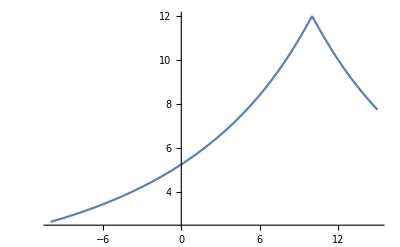

```mathematica
Plot[plot[10],{μ,-10,15}]
```

Posterior P(μ|x) for one datum from Xn = -27

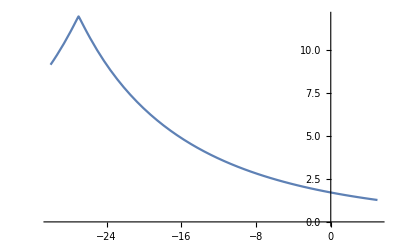

```mathematica
Plot[plot[-27],{μ,-30,5}]
```

Posterior P(μ|x) for all 7 data

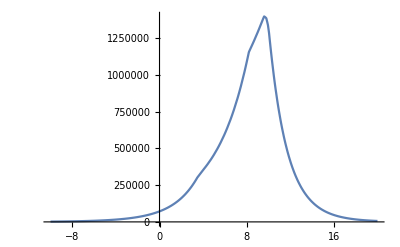

```mathematica
Plot[plot[-27]plot[3.6]plot[8.2]plot[9.8]plot[9.6]plot[9.95]plot[10.05],{μ,-10,20}]
```

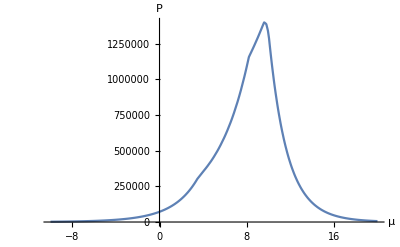

```mathematica
Show[%67,AxesLabel->{HoldForm[μ],HoldForm[P]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

check a small bump around μ=-27

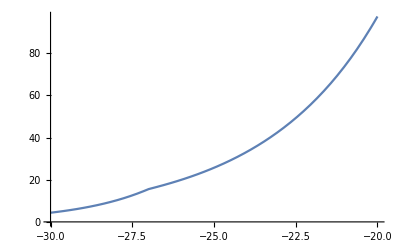

```mathematica
Plot[plot[-27]plot[3.6]plot[8.2]plot[9.8]plot[9.6]plot[9.95]plot[10.05],{μ,-30,-20}]
```

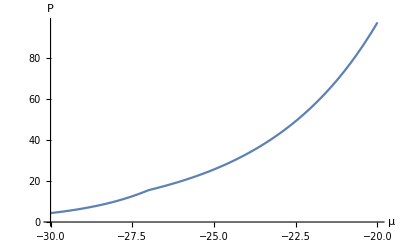

```mathematica
Show[%64,AxesLabel->{HoldForm[μ],HoldForm[P]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```